```mathematica
Clear[Ν,X,Y,Z,H,Ι,J,λ,Κ,s];
```

```mathematica
(* Physical constants *)
k=1.38065 10^-23;
T=Quantity[15.5 10^-3,"Kelvin"];
ℏ=6.62607 10^-34;
β=1/(k T);
```

```mathematica
(* D Wave anneal parameters *)
DWaveAnnealingSchedule=Import["~/Documents/LANLA/DWaveAnnealingSchedule.csv"][[;;,1;;3]];
AnnealParameter=DWaveAnnealingSchedule[[;;,1]];
A=10^9 DWaveAnnealingSchedule[[;;,2]];     (* units in GHz *)
B=10^9 DWaveAnnealingSchedule[[;;,3]];
```

```mathematica
(* Pauli Matrices *)
Ν=5;
X=Table[
Apply[KroneckerProduct][
Table[
If[k==j,PauliMatrix[1],IdentityMatrix[2]],{k,1,Ν}]
],{j,1,Ν}];
Y=Table[
Apply[KroneckerProduct][
Table[
If[k==j,PauliMatrix[2],IdentityMatrix[2]],{k,1,Ν}]
],{j,1,Ν}];
Z=Table[
Apply[KroneckerProduct][
Table[
If[k==j,PauliMatrix[3],IdentityMatrix[2]],{k,1,Ν}]
],{j,1,Ν}];


(* Definition of D Wave Hamiltonian *)

Clear[J,Κ]
λ[Ν_,{J_,Κ_}]=Which[OddQ[Ν],

Table[If[k==⌊Ν/2⌋ ∨ k==⌈Ν/2⌉,J,Κ],{k,1,Ν-1}],

EvenQ[Ν],

Table[If[k==Ν/2∨ k==Ν/2+1,J,Κ],{k,1,Ν-1}]
];

H[s_,{Ι_,J_,Κ_}]:=Module[{sRescaled},
sRescaled=Max[1,Round[Length[AnnealParameter]s]];

2π (A[[sRescaled]]/2∑_(k=1)^Ν X[[k]]-B[[sRescaled]]/2(-Ι Z[[-1]].Z[[1]]+∑_(k=1)^(Ν-1) λ[Ν,{J,Κ}][[k]]Z[[k]].Z[[k+1]]))

];
```

```mathematica
H[0.5,{.2,.3,1}]//MatrixForm
```

(-2.45044×10^10 | 4.24115×10^9 | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4.24115×10^9 | -8.16814×10^9 | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4.24115×10^9 | 0. | 2.04204×10^9 | 4.24115×10^9 | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 4.24115×10^9 | 4.24115×10^9 | -2.24624×10^10 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4.24115×10^9 | 0. | 0. | 0. | -1.22522×10^10 | 4.24115×10^9 | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 4.24115×10^9 | 0. | 0. | 4.24115×10^9 | 4.08407×10^9 | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 2.04204×10^9 | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 4.24115×10^9 | -2.24624×10^10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.04204×10^9 | 4.24115×10^9 | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 1.83783×10^10 | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 2.85885×10^10 | 4.24115×10^9 | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 4.24115×10^9 | 4.08407×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 2.04204×10^9 | 4.24115×10^9 | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 4.24115×10^9 | 1.83783×10^10 | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 1.63363×10^10 | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 4.24115×10^9 | -8.16814×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9
4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -8.16814×10^9 | 4.24115×10^9 | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 1.63363×10^10 | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 1.83783×10^10 | 4.24115×10^9 | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 4.24115×10^9 | 2.04204×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.08407×10^9 | 4.24115×10^9 | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 4.24115×10^9 | 2.85885×10^10 | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 1.83783×10^10 | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 4.24115×10^9 | 2.04204×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.24624×10^10 | 4.24115×10^9 | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 2.04204×10^9 | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 4.08407×10^9 | 4.24115×10^9 | 0. | 0. | 4.24115×10^9 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 4.24115×10^9 | -1.22522×10^10 | 0. | 0. | 0. | 4.24115×10^9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | -2.24624×10^10 | 4.24115×10^9 | 4.24115×10^9 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 4.24115×10^9 | 2.04204×10^9 | 0. | 4.24115×10^9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 0. | -8.16814×10^9 | 4.24115×10^9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.24115×10^9 | 0. | 0. | 0. | 4.24115×10^9 | 0. | 4.24115×10^9 | 4.24115×10^9 | -2.45044×10^10)

```mathematica
(* Redfield quantities *)
τ=Quantity[10^-40,"Seconds"];
ηMRT=0.24;
η[s_]:=Module[{sRescaled},
sRescaled=Max[1,Round[Length[AnnealParameter]s]];
ηMRT B[[sRescaled]]/B[[-1]]];
ΓRedfield[s_,{Ι_,J_,Κ_}]:=c[s,{Ι,J,Κ}]/ℏ^2 S[ω[s,{Ι,J,Κ}],s];
S[ω_,s_]:=ℏ^2(η[s] ω Exp[-ω τ])/(1-Exp[-ℏ ω/(k T)]);
c[s_,{Ι_,J_,Κ_}]:=

1/4∑_(k=1)^Ν Abs[ψ[s,{Ι,J,Κ}][[1]].Z[[k]].ψ[s,{Ι,J,Κ}][[3]]]^2;

ω[s_,{Ι_,J_,Κ_}]:=Quantity[Ε[s,{Ι,J,Κ}][[3]]-Ε[s,{Ι,J,Κ}][[1]],"Hertz"];

Ε[s_,{Ι_,J_,Κ_}]:=Module[{ϵ,ϕ},

{ϵ,ϕ}=Eigensystem[H[s,{Ι,J,Κ}]];
{ϵ,ϕ}={ϵ[[#]],ϕ[[#]]}&@Ordering[ϵ];

ϵ
];
ψ[s_,{Ι_,J_,Κ_}]:=Module[{ϵ,ϕ},

{ϵ,ϕ}=Eigensystem[H[s,{Ι,J,Κ}]];
{ϵ,ϕ}={ϵ[[#]],ϕ[[#]]}&@Ordering[ϵ];

ϕ
];
```

```mathematica
(* DON'T TOUCH THESE INTERFACES UNLESS N ≤ 5 !! *)
Κ=1;  Ι=0.2;
Manipulate[ListLogPlot[tQA ΓRedfield[#,{Ι,J,Κ}]&/@Range[.5,1,.02],PlotRange->{0.001,10^8},DataRange->{.5,1}],{{J,0.24},{.24,.28,.32,.36,.4}},{{tQA,5},{5,100,250,500,2000}}]
Manipulate[ListPlot[c[#,{Ι,J,Κ}]&/@Range[0,1,.01],PlotRange->{0,1},Joined->True,DataRange->{0,1},AxesLabel->{"s"}],{J,{.24,.28,.32,.36,.4}}]
```

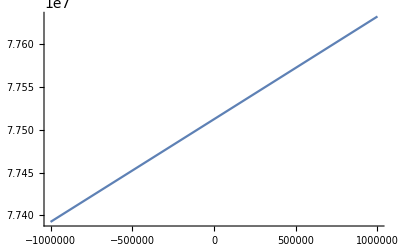

```mathematica
Plot[(η[1] ω)/(1-Exp[-QuantityMagnitude[ℏ] ω/QuantityMagnitude[(k T)]]),{ω,-10^6, 10^6}]
```

```mathematica
(* REDFIELD MASTER EQUATION PREDICTIONS *)
```

{39.73457,Null}

Computed Redfield Rate

{6.62372,Null}

Computed Thermal Population

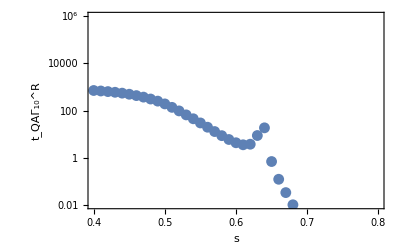

```mathematica
tQA=Quantity[5 10^-6,"Seconds"];
J=.24; Ι=.2; Κ=1;
dataRate=tQA ΓRedfield[#,{Ι,J,Κ}]&/@Range[.4,.8,.01];//AbsoluteTiming
Print["Computed Redfield Rate"]
dataPop=(1-Exp[-ℏ ω[#,{Ι,J,Κ}]/(k T)])&/@Range[.4,.8,.01];//AbsoluteTiming
Print["Computed Thermal Population"]
ListLogPlot[{dataRate,dataGap1,dataGap2},PlotRange->{10^-2,10^6},DataRange->{.4,.8},AxesLabel->{"s","t_QAΓ_10^R"},PlotTheme->"Detailed"]
```

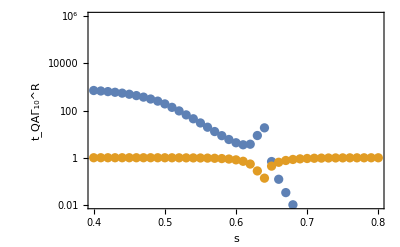

```mathematica
ListLogPlot[{dataRate,dataPop},PlotRange->{10^-2,10^6},DataRange->{.4,.8},AxesLabel->{"s","t_QAΓ_10^R"},PlotTheme->"Detailed"]
```

```mathematica
ImportSuccessProbabilities[5,24,.24]
```

{0.392667,0.019672}

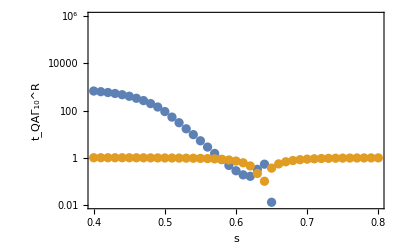

{6.51197,Null}

Computed Thermal Population

{3.57524,Null}

{3.53428,Null}

Computed Excitation Gap

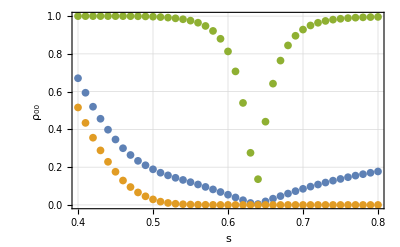

```mathematica
J=.24; Ι=.2; Κ=1;
dataPop=(1-Exp[-ℏ ω[#,{Ι,J,Κ}]/(k T)])&/@Range[.4,.8,.01];//AbsoluteTiming
Print["Computed Thermal Population"]
dataGap1=10^-10(Ε[#,{Ι,J,Κ}][[3]]-Ε[#,{Ι,J,Κ}][[1]])&/@Range[.4,.8,.01];//AbsoluteTiming
dataGap2=10^-10(Ε[#,{Ι,J,Κ}][[2]]-Ε[#,{Ι,J,Κ}][[1]])&/@Range[.4,.8,.01];//AbsoluteTiming
Print["Computed Excitation Gap"]
ListPlot[{dataGap1,dataGap2,dataPop},PlotRange->{0,1},DataRange->{.4,.8},AxesLabel->{"s","ρ_00"},PlotTheme->"Detailed"]
```

```mathematica
ω[.64,{Ι,J,Κ}]
```

4.7354×10^7

```mathematica
Γ=Abs[tQA (.62-.6)/(ω[.62,{Ι,J,Κ}]-ω[.6,{Ι,J,Κ}])(1/2 ω[.64,{Ι,J,Κ}])^2]
```

0.19293

```mathematica
ⅇ^(-2π Γ)
```

2.61081×10^-211

```mathematica
ImportSuccessProbabilities[2000,8,.24]
```

{0.404863,0.0210533}

```mathematica
J=.24; Ι=.2; Κ=1;
dataPop9=(1-Exp[-ℏ ω[#,{Ι,J,Κ}]/(k T)])&/@Range[.4,.8,.01];//AbsoluteTiming
```

{20.15134,Null}

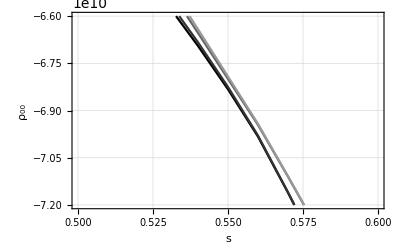

```mathematica
ListPlot[Transpose[Ε[#,{Ι,J,Κ}][[;;4]]&/@Range[.5,.6,.01]],DataRange->{.5,.6},AxesLabel->{"s","ρ_00"},PlotTheme->"Detailed",PlotStyle->(RGBColor[#,#,#]&/@{0,.2,.4,.6}),PlotRange->{-7.2 10^10,-6.6 10^10},Joined->True]
```

```mathematica
ImportSuccessProbabilities[5,8,.24]
```

{0.306471,0.0181421}

```mathematica
ImportSuccessProbabilities[AnnTime_,NumQubits_,JCoupling_]:=Module[
{NumSuccesses,NumFailures,SuccessProbs,FailureProbs,MeanSuccess,MeanFailure,StdDevSuccess,StdDevFailure},
{NumSuccesses,NumFailures}=Transpose@Import["~/Documents/LANLA/data/I=0.2_J="<>ToString[JCoupling]<>"_N="<>ToString[NumQubits]<>"_Type=2_AnnTime="<>ToString[AnnTime]<>".mat"][[1,1,;;,1,1,1,{2,3}]];
{SuccessProbs,FailureProbs}=#/1000&/@{NumSuccesses,NumFailures};
{MeanSuccess,MeanFailure}=Mean[#]&/@{SuccessProbs,FailureProbs};
{StdDevSuccess,StdDevFailure}=StandardDeviation[#]&/@{SuccessProbs,FailureProbs};
{MeanSuccess,StdDevSuccess}
];
```

```mathematica
Exp[-ℏ ω[1,{Ι,J,Κ}]/(k T)]
```

0.0000543039

```mathematica
-ℏ ω[1,{Ι,J,Κ}]/(k T)
```

-9.82092